## Initialize

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\trajectory in mosaic aggregates\\props.m";
```

## Brachyury Flow

### video B7

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\B7\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg.tif"];
masks= Import[dir<>"masks.tif"];
```

```mathematica
Manipulate[HighlightImage[images[[i]],masks[[i]]],{i,1,Length@images,1}]
```

```mathematica
Manipulate[Threshold[images[[i]]*masks[[i]],{"LargestValues",5000}],{i,1,Length@images,1}]
```

```mathematica
inCent=centroidsIntensityM2[images,masks,5000];
```

```mathematica
Rasterize[coloredTraj[inCent,0.075],"Graphics",ImageResolution->200]
```

-Graphics-

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

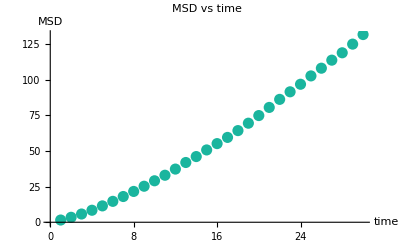

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

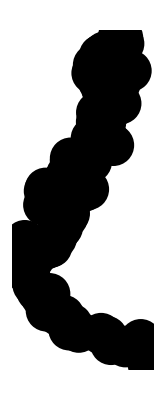

```mathematica
Show[Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.04],Point@movAvg}],coloredTraj[inCent,0.075]]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean[distance]
```

0.609303

```mathematica
dist=FindDistribution[distance]
```

MixtureDistribution[{0.186694,0.654864,0.158442},{NormalDistribution[0.215103,0.0588403],NormalDistribution[0.624242,0.173936],NormalDistribution[1.04042,0.342524]}]

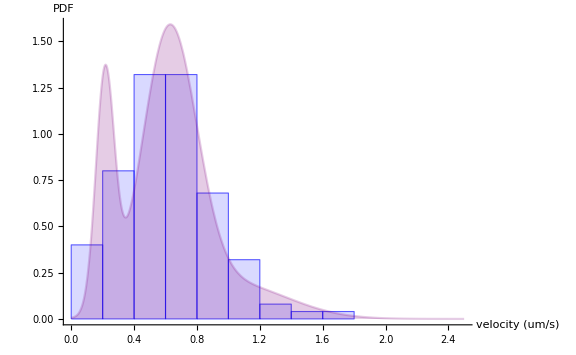

```mathematica
histogramDist[distance,dist,2.5]
```

### video C8

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\C8\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg.tif"][[;;-12]];
masks=Import[dir<>"masks.tif"][[;;-12]];
```

```mathematica
Manipulate[HighlightImage[images[[i]],masks[[i]]],{i,1,Length@images,1}]
```

```mathematica
Manipulate[Threshold[images[[i]]*masks[[i]],{"LargestValues",2000}],{i,1,Length@images,1}]
```

```mathematica
inCent=centroidsIntensityM2[images,masks,2000];
```

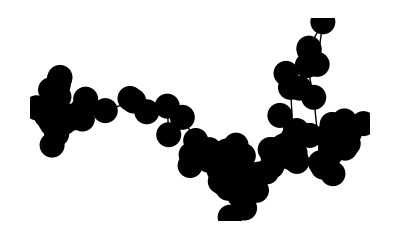

```mathematica
coloredTraj[inCent,0.045]
```

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

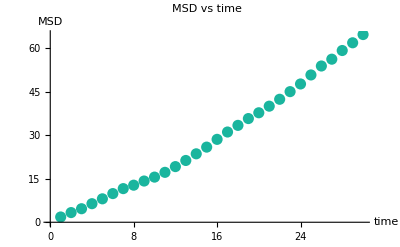

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

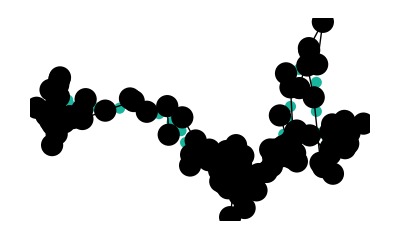

```mathematica
Show[Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.02],Point@movAvg}],coloredTraj[inCent,0.04]]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean@distance
```

0.475658

```mathematica
dist=FindDistribution[distance]
```

LogNormalDistribution[-0.937196,0.666655]

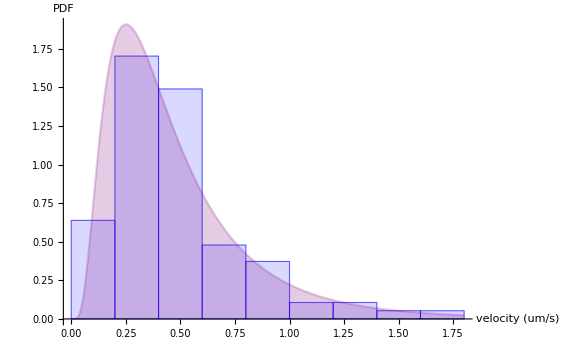

```mathematica
histogramDist[distance,dist,1.8]
```

### video C10

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\C10\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg.tif"];
masks=Import[dir<>"masks.tif"];
```

```mathematica
Manipulate[HighlightImage[images[[i]],masks[[i]]],{i,1,Length@images,1}]
```

```mathematica
Manipulate[Threshold[images[[i]]*masks[[i]],{"LargestValues",5000}],{i,1,Length@images,1}]
```

```mathematica
inCent=centroidsIntensityM2[images,masks,5000];
```

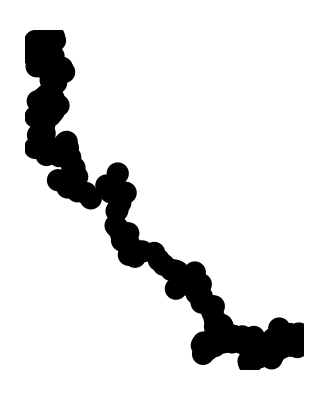

```mathematica
coloredTraj[inCent,0.04]
```

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

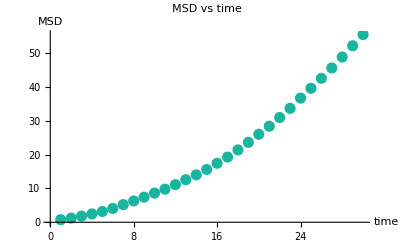

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

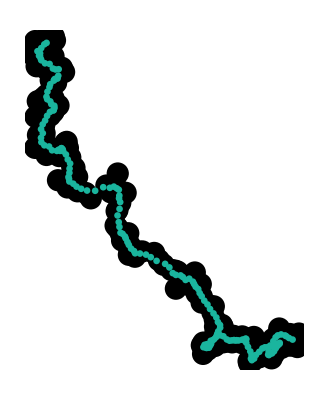

```mathematica
Show[coloredTraj[inCent,0.04],Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.012],Point@movAvg}]]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean@distance
```

0.325473

```mathematica
dist=FindDistribution[distance]
```

WeibullDistribution[2.26666,0.368118]

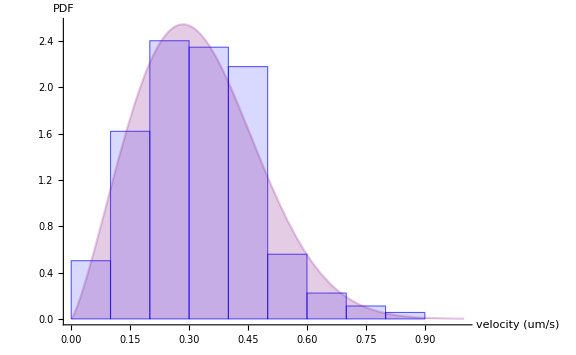

```mathematica
histogramDist[distance,dist]
```

### video D7

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\D7\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg.tif"];
masks = Import[dir<>"masks.tif"];
```

```mathematica
Manipulate[HighlightImage[images[[i]],masks[[i]]],{i,1,Length@images,1}]
```

```mathematica
Manipulate[Threshold[images[[i]]*masks[[i]],{"LargestValues",2000}],{i,1,Length@images,1}]
```

```mathematica
inCent=centroidsIntensityM2[images,masks,2000];
```

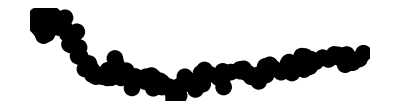

```mathematica
coloredTraj[inCent,0.030]
```

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

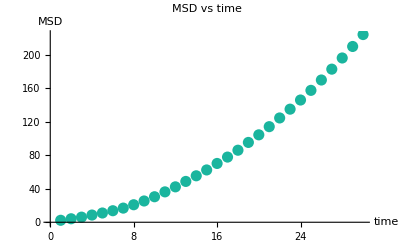

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

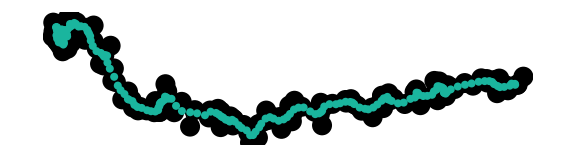

```mathematica
Show[coloredTraj[inCent,0.025],Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.01],Point@movAvg}],ImageSize-> Large]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean@distance
```

0.585262

```mathematica
dist=FindDistribution[distance]
```

WeibullDistribution[1.89181,0.662263]

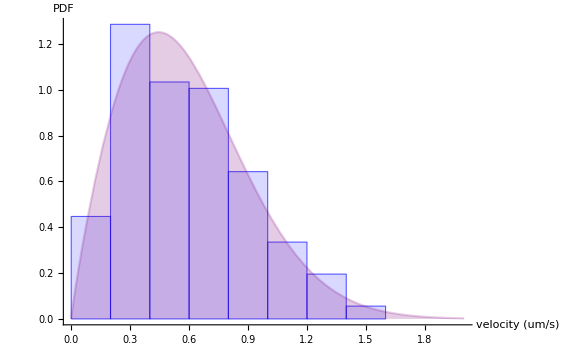

```mathematica
histogramDist[distance,dist,2.0]
```

### video D11

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\D11\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg.tif"];
masks=Import[dir<>"masks.tif"];
```

```mathematica
Manipulate[HighlightImage[images[[i]],masks[[i]]],{i,1,Length@images,1}]
```

```mathematica
Manipulate[Threshold[images[[i]]*masks[[i]],{"LargestValues",2000}],{i,1,Length@images,1}]
```

```mathematica
inCent=centroidsIntensityM2[images,masks,2000];
```

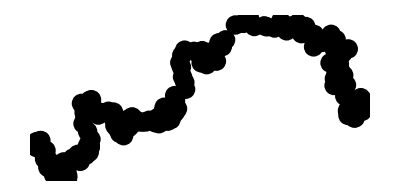

```mathematica
coloredTraj[inCent,0.035]
```

```mathematica
images~trajVid~inCent
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

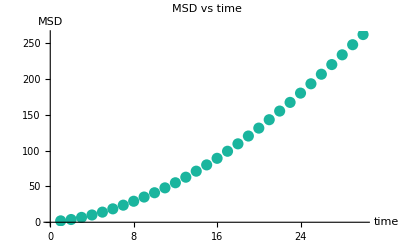

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

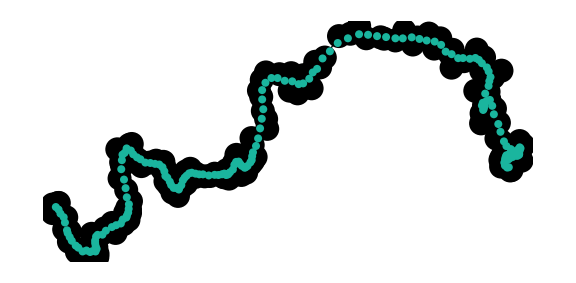

```mathematica
Show[coloredTraj[inCent,0.03],Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.01],Point@movAvg}],ImageSize->Large]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean@distance
```

0.663499

```mathematica
dist= FindDistribution[distance]
```

GammaDistribution[3.27737,0.2031]

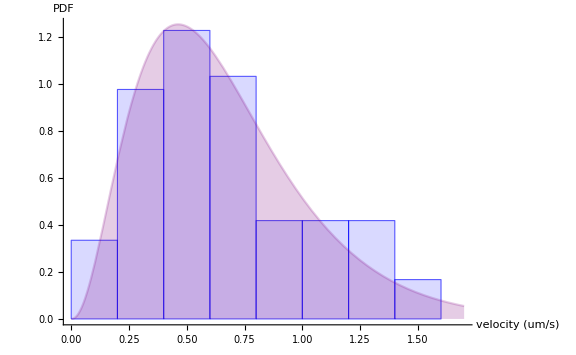

```mathematica
histogramDist[distance,dist,1.7]
```

### video E10

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\E10\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg.tif"];
masks=Import[dir<>"masks.tif"];
```

```mathematica
Manipulate[HighlightImage[images[[i]],masks[[i]]],{i,1,Length@images,1}]
```

```mathematica
Manipulate[Threshold[images[[i]]*masks[[i]],{"LargestValues",5000}],{i,1,Length@images,1}]
```

```mathematica
inCent=centroidsIntensityM2[images,masks,5000];
```

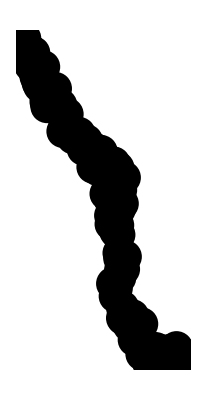

```mathematica
coloredTraj[inCent,0.06]
```

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

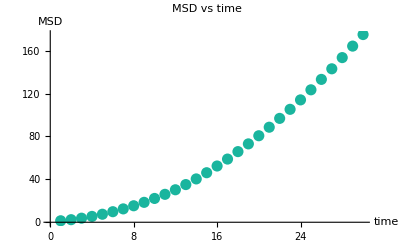

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

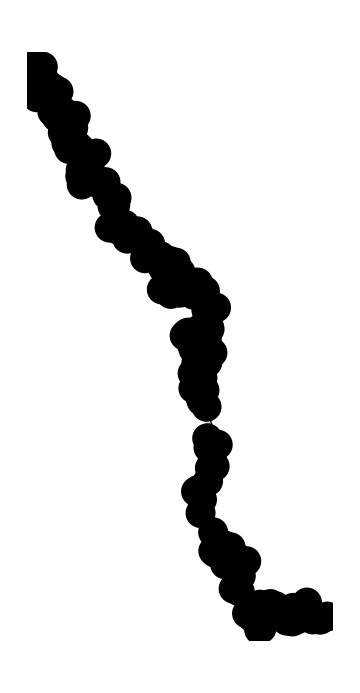

```mathematica
Show[Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.02],Point@movAvg}],coloredTraj[inCent,0.06], ImageSize->Medium]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
dist=FindDistribution[distance]
```

ExtremeValueDistribution[0.360925,0.203162]

```mathematica
Mean@distance
```

0.477694

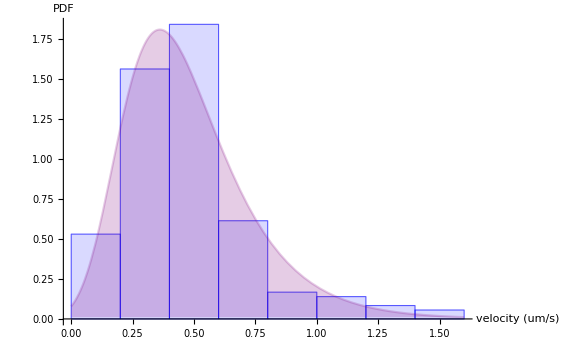

```mathematica
histogramDist[distance,dist,1.6]
```

### video F10

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\F10\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg.tif"];
masks=Import[dir<>"masks.tif"];
```

```mathematica
Manipulate[HighlightImage[images[[i]],masks[[i]]],{i,1,Length@images,1}]
```

```mathematica
Manipulate[Threshold[images[[i]]*masks[[i]],{"LargestValues",5000}],{i,1,Length@images,1}]
```

```mathematica
inCent=centroidsIntensityM2[images,masks,5000];
```

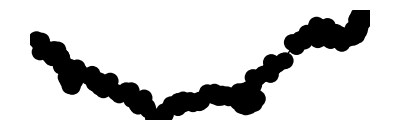

```mathematica
coloredTraj[inCent,0.03]
```

```mathematica
images~trajVid~inCent
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

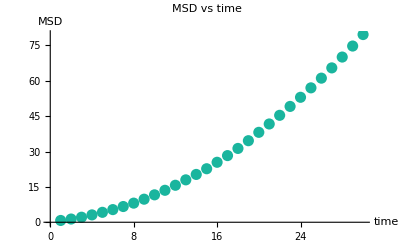

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

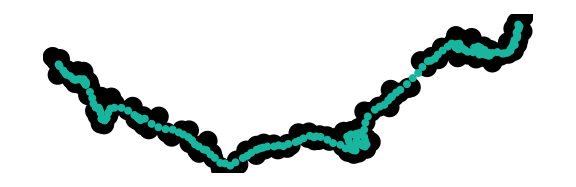

```mathematica
Show[coloredTraj[inCent,0.025],Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.01],Point@movAvg}], ImageSize->Large]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
dist=FindDistribution[distance]
```

BetaDistribution[2.07327,3.54981]

```mathematica
Mean@distance
```

0.367199

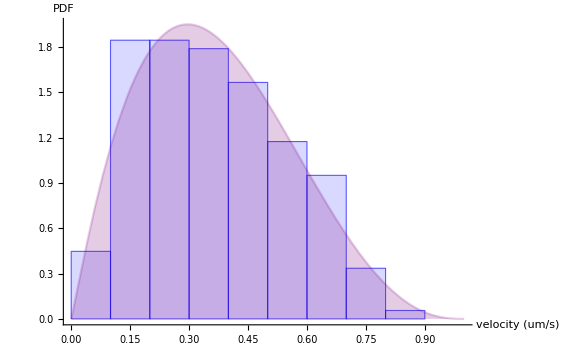

```mathematica
histogramDist[distance,dist,1.0]
```

## MSD plot and velocity distribution

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\trajectory in mosaic aggregates\\Brachyury_motion_2.mx";
```

```mathematica
acquistionPeriod=6;
```

```mathematica
timesteps=Ceiling[0.20(Map[Length]@saved //Mean)]
```

33

```mathematica
msds=MSD[#,timesteps,"M2"]&/@saved;
```

```mathematica
(* since the timelapse images were binned 2x2, acquisition time 6 minutes *)
```

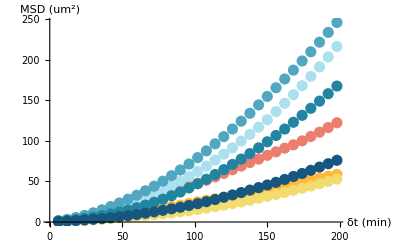

```mathematica
ListPlot[Thread[{Range@Length@# *acquistionPeriod,#*2*(0.633)^2}]&/@msds,PlotStyle->ColorData[24],AxesLabel->{Style["δt (min)",{Bold,15}],
Style["MSD (um^2)",{Bold,15}]},AxesStyle->Directive[Black, 14]]/.PointSize[_]:> PointSize[0.02]
```

```mathematica
velocities= Flatten[EuclideanDistance@@#&/@Partition[#,2,1]&/@saved,1]/acquistionPeriod;
```

```mathematica
dist=FindDistribution@velocities
```

GammaDistribution[2.76125,0.0647088]

```mathematica
meanvelocity=Mean@dist
```

0.178677

```mathematica
Rasterize[histogramDist[velocities,dist,0.8],"Graphics",ImageResolution->800]
```

-Graphics-